```mathematica
(**Size of the interval**)
```

```mathematica
lambda=3
```

3

```mathematica
(**Definition of the test function**)
```

```mathematica
u[x_]:=If[x^2<lambda^2,1/Sqrt[-Log[(lambda^2-x^2)/(2*lambda^2)]],0]
```

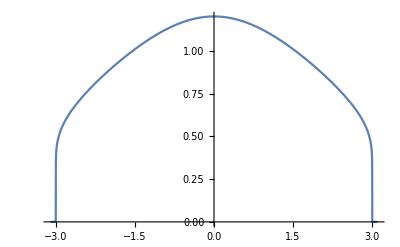

```mathematica
Plot[u[x],{x,-lambda-0.1,lambda+0.1},PlotRange->All]
```

```mathematica
(**Definition of the Logarithmic Laplacian**)
```

```mathematica
rho1=2*Log[2]+Gamma'[1/2]/Gamma[1/2]-EulerGamma
```

-EulerGamma+2 Log[2]+PolyGamma[0,1/2]

```mathematica
LapLog[x_]:=NIntegrate[(u[x]-u[y])/Abs[x-y],{y,x-1,x+1}]-NIntegrate[u[y]/Abs[x-y],{y,-Infinity,x-1}]-NIntegrate[u[y]/Abs[x-y],{y,x+1,Infinity}]+rho1*u[x]
```

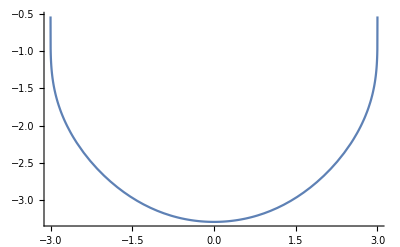

```mathematica
B=Plot[LapLog[x],{x,-lambda,lambda},PlotRange->All]
```

```mathematica
(**Number of subintervals for the mesh**)
```

```mathematica
n=50;
```

```mathematica
(**Value of the logarithmic Laplacian at (almost) the ends of the interval**)
```

```mathematica
ll1=LapLog[-lambda+0.00000000001];
```

```mathematica
(**Table of values for the logarithmic Laplacian**)
```

```mathematica
l=Table[{N[-lambda+m(2*lambda/(n+1))],LapLog[-lambda+m(2*lambda/(n+1))]},{m,1,n}];
l=Append[l,{lambda,ll1}];
l=Prepend[l,{-lambda,ll1}];
```

```mathematica
(**Command to export the Table to a file recognized by MatLab**)
```

```mathematica
Export["~/Desktop/file50_lambda3.txt",l,"Table"];
```